Generates real space Fermi Arc

The dat files are generated in the directory RealSpaceFermiArcPlots. They can be plotted with RealSpaceFermiArcs.nb

```mathematica
tStart=AbsoluteTime[];
```

```mathematica
Clear[Lx,Ly,A,
sx3d,SX3D,sx3dp,SX3DP,
sy3d,SY3D,sy3dp,SY3DP,
sz3d,SZ3D,sz3dp,SZ3DP,
cx3d,CX3D,cx3dp,CX3DP,
cy3d,CY3D,cy3dp,CY3DP,
cz3d,CZ3D,cz3dp,CZ3DP,
cons,Cons]
```

```mathematica
Lx=16;
Ly=16;
Lz =19;
A=Lx*Ly*Lz;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sx3d[j+k Lx+l Lx Ly,j+1+k Lx + l Lx Ly]=-I/2,sx3d[j+1+k Lx + l Lx Ly,j+k Lx+l Lx Ly]=I/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

SX3D=Table[sx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx3dp[i_Integer,j_Integer]=0;

Do[Do[{sx3dp[(k+1)Lx+ l Lx Ly,1+k Lx+ l Lx Ly]=-I/2,sx3dp[1+k Lx+ l Lx Ly,(k+1)Lx+ l Lx Ly]=I/2},{k,0,Ly-1}],{l,0,Lz-1}]

SX3DP=Table[sx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=-I/2,sy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

SY3D=Table[sy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy3dp[i_Integer,j_Integer]=0;

Do[Do[{sy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=-I/2,sy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{l,0,Lz-1}]

SY3DP=Table[sy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cx3d[j+k Lx+l Lx Ly,j+1+k Lx+l Lx Ly]=1/2,cx3d[j+1+k Lx+l Lx Ly,j+k Lx+l Lx Ly]=1/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

CX3D=Table[cx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx3dp[i_Integer,j_Integer]=0;

Do[Do[{cx3dp[(1+k)Lx+l Lx Ly,1+k Lx+l Lx Ly]=1/2,cx3dp[1+k Lx+l Lx Ly,(1+k)Lx+l Lx Ly]=1/2},{k,0,Ly-1}],{l,0,Lz-1}]

CX3DP=Table[cx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=1/2,cy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

CY3D=Table[cy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy3dp[i_Integer,j_Integer]=0;

Do[Do[{cy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=1/2,cy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{l,0,Lz-1}]

CY3DP=Table[cy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cz3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cz3d[j+(k-1) Lx+(l-1) Lx Ly,j+(k-1)Lx+l Lx Ly]=1/2,cz3d[j+(k-1)Lx+l Lx Ly,j+(k-1) Lx+(l-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}],{l,1,Lz-1}]

CZ3D=Table[cz3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cz3dp[i_Integer,j_Integer]=0;

Do[Do[{cz3dp[(k-1)Lx+j+(Lz-1) Lx Ly,(k-1)Lx+j]=1/2,cz3dp[(k-1)Lx+j,(k-1)Lx+j+(Lz-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}]

CZ3DP=Table[cz3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0;

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,tz_,αx_,αy_,αz_]:=t*(KroneckerProduct[SX3D+αx*SX3DP,σ1]+KroneckerProduct[SY3D+αy*SY3DP, σ2])+KroneckerProduct[2*Cons-2t0*(CX3D+CY3D+αx*CX3DP+αy*CY3DP),σ3]+KroneckerProduct[tz *(CZ3D + αz*CZ3DP)-m*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals2D=Dimensions[FlatSite][[1]]
```

512

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals2D,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/3)*(x-1)+8
LineDn[x_]:=(2/3)*(x-2)+6
```

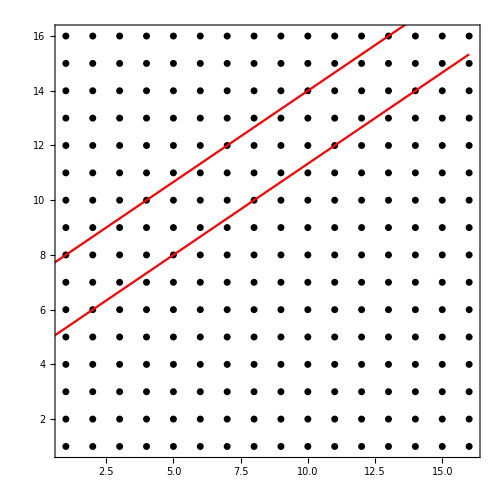

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist2D=Sort[FibonupNew];
```

```mathematica
Clear[XList,YList,ZList,zzz1,XList2D,YList2D]
```

```mathematica
XList2D =Mod[Fibonlist2D,Lx,1];
```

```mathematica
YList2D =Ceiling[Fibonlist2D/Lx];
```

```mathematica
Dimensions[XList2D]
```

{35}

```mathematica
XList = {};
YList={};
ZList = {};
```

```mathematica
Do[XList = Append[XList,XList2D ],{n,1,Lz}]
```

```mathematica
XList = Flatten[XList];
```

```mathematica
Do[YList = Append[YList,YList2D ],{n,1,Lz}]
```

```mathematica
YList = Flatten[YList];
```

```mathematica
zzz1 = Table[1,{n,1,Dimensions[XList2D][[1]]}];
```

```mathematica
Do[ZList = Append[ZList,zzz1 * m],{m,1,Lz}]
```

```mathematica
ZList = Flatten[ZList];
```

```mathematica
Fibonlist={};
```

```mathematica
Do[Fibonlist = Append[Fibonlist,Fibonlist2D+n*Lx*Ly],{n,0,Lz-1}];
```

```mathematica
Fibonlist;
```

```mathematica
Fibonlist=Sort[Flatten[Fibonlist]];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]];
```

```mathematica
NOrbitalsQuasi2D = NOrbitalsQuasi/Lz;
```

```mathematica
NOrbitalsOutside = NOrbitals2D*Lz-NOrbitalsQuasi;
```

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.136719

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianWSM[1.,0.5,0,1,0,0,0];
```

```mathematica
Dimensions[HTrial];
```

```mathematica
Clear[sx3d,SX3D,sx3dp,SX3DP,
sy3d,SY3D,sy3dp,SY3DP,
sz3d,SZ3D,sz3dp,SZ3DP,
cx3d,CX3D,cx3dp,CX3DP,
cy3d,CY3D,cy3dp,CY3DP,
cz3d,CZ3D,cz3dp,CZ3DP,
cons,Cons]
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
Clear[Hfbfb]
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
Clear[H2d2d]
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
Clear[H2dfb]
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
Clear[Hfb2d]
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D] (** To save memory **)
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

```mathematica
Clear[datDensity,MidEigvec1, MidEigvec2]
```

```mathematica
MidEigvec1 = ValVecFibon[[NOrbitalsQuasi/2]][[2]] ;
```

```mathematica
MidEigvec2 = ValVecFibon[[NOrbitalsQuasi/2 + 1]][[2]];
```

```mathematica
(** Divide the last term by 2 for normalization **)
```

```mathematica
datDensity = Table[{XList[[m]],YList[[m]],ZList[[m]],(Abs[MidEigvec1[[2*m]]]^2 + Abs[MidEigvec1[[2*m-1]]]^2 + Abs[MidEigvec2[[2*m]]]^2 + Abs[MidEigvec2[[2*m-1]]]^2)/2 },{m,1,NOrbitalsQuasi/2}];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@datDensity[[All,4]];
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon={};
```

```mathematica
Do[Do[TabDataFibon=Append[TabDataFibon,{Mod[i,NOrbitalsQuasi2D/2,1],z,
(Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2)/2

}],{i,1+(z-1)*NOrbitalsQuasi2D/2,NOrbitalsQuasi2D/2+(z-1)*NOrbitalsQuasi2D/2}],{z,1,Lz}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
(** Divide the last term by 2 for normalization **)
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]},{i,1,3*NOrbitalsQuasi/2,3}];
```

Exports the file

```mathematica
Export["RealSpaceFermiArcPlots/LDOSFermiArcReal_161619_Rational_3D_Up+6_Dn+4.dat",TabFibonacci];
```

```mathematica
tStop=AbsoluteTime[];
```

```mathematica
timeTakenInSeconds = tStop-tStart
```